#### Potencial que tem os autoestados os 2 barions reais https://community.wolfram.com/groups/-/m/t/3311726

```mathematica
ClearAll["Global`*"]
```

```mathematica
Dados={1876.54,2378.0,2464.0,4908.0,11632.0,1876.54,1879.14,2231.36,4572.92,11240.4,2231.36,2378.74,2629.72,4941.7,11583.8,4572.92,4908.0,4941.7,7243.1,13840.0,11240.4,11583.8,11632.0,11614.0,13840.0,1876.54,1879.14,2231.36,4572.92,11240.4,1879.14,2394.9,2464.0,4909.6,11624.0,2231.36,2394.9,2643.42,4941.6,11584.8,4572.92,4909.6,4941.6,7239.94,13800.0,11240.4,11584.8,11624.0,13800.0,20845.4,2231.36,2378.74,2629.72,4941.7,11583.8,2231.36,2394.9,2643.42,4941.6,11584.8,2629.72,2643.42,3344.9,5387.2,12091.6,5387.2,4941.7,4941.6,7580.0,14100.0,11583.8,11584.8,12091.6,14100.0,20320.0,4572.92,4908.0,4941.7,7243.1,13840.0,4572.92,4909.6,4941.6,7239.94,13800.0,4941.7,4941.6,5387.2,7580.0,14100.0,5387.2,7239.94,7243.1,9590.0,13900.0,13800.0,13840.0,13900.0,14100.0,21800.0,11240.4,11583.8,11614.0,11632.0,13840.0,11240.4,11584.8,11624.0,13800.0,20845.4,11583.8,11584.8,12091.6,14100.0,20320.0,13800.0,13840.0,13900.0,14100.0,21800.0,11614.0,20320.0,20845.4,21800.0,28742.0}
```

{1876.54,2378.,2464.,4908.,11632.,1876.54,1879.14,2231.36,4572.92,11240.4,2231.36,2378.74,2629.72,4941.7,11583.8,4572.92,4908.,4941.7,7243.1,13840.,11240.4,11583.8,11632.,11614.,13840.,1876.54,1879.14,2231.36,4572.92,11240.4,1879.14,2394.9,2464.,4909.6,11624.,2231.36,2394.9,2643.42,4941.6,11584.8,4572.92,4909.6,4941.6,7239.94,13800.,11240.4,11584.8,11624.,13800.,20845.4,2231.36,2378.74,2629.72,4941.7,11583.8,2231.36,2394.9,2643.42,4941.6,11584.8,2629.72,2643.42,3344.9,5387.2,12091.6,5387.2,4941.7,4941.6,7580.,14100.,11583.8,11584.8,12091.6,14100.,20320.,4572.92,4908.,4941.7,7243.1,13840.,4572.92,4909.6,4941.6,7239.94,13800.,4941.7,4941.6,5387.2,7580.,14100.,5387.2,7239.94,7243.1,9590.,13900.,13800.,13840.,13900.,14100.,21800.,11240.4,11583.8,11614.,11632.,13840.,11240.4,11584.8,11624.,13800.,20845.4,11583.8,11584.8,12091.6,14100.,20320.,13800.,13840.,13900.,14100.,21800.,11614.,20320.,20845.4,21800.,28742.}

```mathematica
BarDat=Partition[Dados,5]
```

{{1876.54,2378.,2464.,4908.,11632.},{1876.54,1879.14,2231.36,4572.92,11240.4},{2231.36,2378.74,2629.72,4941.7,11583.8},{4572.92,4908.,4941.7,7243.1,13840.},{11240.4,11583.8,11632.,11614.,13840.},{1876.54,1879.14,2231.36,4572.92,11240.4},{1879.14,2394.9,2464.,4909.6,11624.},{2231.36,2394.9,2643.42,4941.6,11584.8},{4572.92,4909.6,4941.6,7239.94,13800.},{11240.4,11584.8,11624.,13800.,20845.4},{2231.36,2378.74,2629.72,4941.7,11583.8},{2231.36,2394.9,2643.42,4941.6,11584.8},{2629.72,2643.42,3344.9,5387.2,12091.6},{5387.2,4941.7,4941.6,7580.,14100.},{11583.8,11584.8,12091.6,14100.,20320.},{4572.92,4908.,4941.7,7243.1,13840.},{4572.92,4909.6,4941.6,7239.94,13800.},{4941.7,4941.6,5387.2,7580.,14100.},{5387.2,7239.94,7243.1,9590.,13900.},{13800.,13840.,13900.,14100.,21800.},{11240.4,11583.8,11614.,11632.,13840.},{11240.4,11584.8,11624.,13800.,20845.4},{11583.8,11584.8,12091.6,14100.,20320.},{13800.,13840.,13900.,14100.,21800.},{11614.,20320.,20845.4,21800.,28742.}}

```mathematica
BarDat[[1]]
```

{1876.54,2378.,2464.,4908.,11632.}

```mathematica
BarDat[[1,5]]
```

11632.

```mathematica
BarTit={"uu","ud","us","uc","ub","du","dd","ds","dc","db","su","sd","ss","sc","sb","cu","cd","cs","cc","cb","bu","bd","bs","bc","bb"}
```

{uu,ud,us,uc,ub,du,dd,ds,dc,db,su,sd,ss,sc,sb,cu,cd,cs,cc,cb,bu,bd,bs,bc,bb}

```mathematica
PotxMax=20.0;
xmax=0.5;
NumRegArq=500;
xstep=(2.0*xmax)/NumRegArq;
PorcCorte=0.95;
ListaCorte={};
```

```mathematica
dressingTransformationPotentials[evals_,xMax_,opts___]:=Module[{ε,f,g,evals1=Sort[evals]-Max[evals],W=0&},Do[ε=evals1[[-k]];
W=NDSolveValue[{f'[x]-f[x]^2+W[x]==ε,f[0]==0,g'[x]==4 f[x] f'[x]-W'[x],g[0]==2 ε-W[0]},{f,g},{x,0,xMax},opts][[2]],{k,2,Length[evals1]}];
Function@@{ξ,W[ξ]+Max[evals]}]
```

#### Loop varredura dos 5 barions

```mathematica
matout=OpenWrite["ResHEP1.csv"];
```

==========   Barion: uu==========

Raio do poco para PotCorte=11050.4 xCorte=0.096

Potencial obtido:

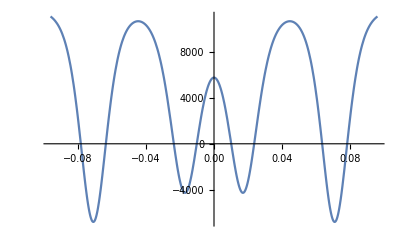

Niveis experimentais:

{1876.54,2378.,2464.,4908.,11632.}

Eigensystem::maxit2: Warning: maximum number of iterations, 1000, has been reached by the Arnoldi algorithm without convergence to the specified tolerance, but the current best computed value has been returned. You can use method options with Method -> {Arnoldi, opts} to increase the size of basis vectors, the maximum number of iterations, reduce the tolerance, or use an estimate as a shift, any of which may help.

Eigensystem::chnpdef: Warning: there is a possibility that the second matrix SparseArray[Automatic,«2»,{1,{{0,«16000»,64001},«1»},{0.000666667,-0.000166667,0.000333333,-0.000166667,0.00133333,-0.000166667,«63989»,0.000333333,0.000333333,0.00266667,0.000333333,0.000333333,0.00266667}}] in the first argument is not positive definite, which is necessary for the Arnoldi method to give accurate results.

Niveis obtidos pela solucao eq Schrodinger com este potencial:

{1877.02,2378.93,2464.91,4908.71,11633.4}

==========   Barion: ud==========

Raio do poco para PotCorte=10678.4 xCorte=0.114

Potencial obtido:

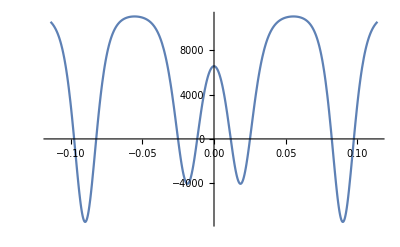

Niveis experimentais:

{1876.54,1879.14,2231.36,4572.92,11240.4}

Eigensystem::maxit2: Warning: maximum number of iterations, 1000, has been reached by the Arnoldi algorithm without convergence to the specified tolerance, but the current best computed value has been returned. You can use method options with Method -> {Arnoldi, opts} to increase the size of basis vectors, the maximum number of iterations, reduce the tolerance, or use an estimate as a shift, any of which may help.

Eigensystem::chnpdef: Warning: there is a possibility that the second matrix SparseArray[Automatic,«2»,{1,{{0,«16000»,64001},«1»},{0.000666667,-0.000166667,0.000333333,-0.000166667,0.00133333,-0.000166667,«63989»,0.000333333,0.000333333,0.00266667,0.000333333,0.000333333,0.00266667}}] in the first argument is not positive definite, which is necessary for the Arnoldi method to give accurate results.

Niveis obtidos pela solucao eq Schrodinger com este potencial:

{1877.54,1880.15,2231.79,4573.53,11241.8}

==========   Barion: us==========

Raio do poco para PotCorte=11004.6 xCorte=0.096

Potencial obtido:

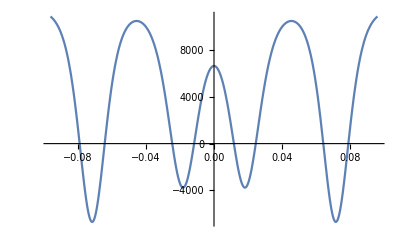

Niveis experimentais:

{2231.36,2378.74,2629.72,4941.7,11583.8}

Eigensystem::maxit2: Warning: maximum number of iterations, 1000, has been reached by the Arnoldi algorithm without convergence to the specified tolerance, but the current best computed value has been returned. You can use method options with Method -> {Arnoldi, opts} to increase the size of basis vectors, the maximum number of iterations, reduce the tolerance, or use an estimate as a shift, any of which may help.

General::stop: Further output of Eigensystem::maxit2 will be suppressed during this calculation.

Eigensystem::chnpdef: Warning: there is a possibility that the second matrix SparseArray[Automatic,«2»,{1,{{0,«16000»,64001},«1»},{0.000666667,-0.000166667,0.000333333,-0.000166667,0.00133333,-0.000166667,«63989»,0.000333333,0.000333333,0.00266667,0.000333333,0.000333333,0.00266667}}] in the first argument is not positive definite, which is necessary for the Arnoldi method to give accurate results.

General::stop: Further output of Eigensystem::chnpdef will be suppressed during this calculation.

Niveis obtidos pela solucao eq Schrodinger com este potencial:

{2232.03,2379.66,2630.4,4942.34,11585.2}

==========   Barion: uc==========

Raio do poco para PotCorte=13148. xCorte=0.102

Potencial obtido:

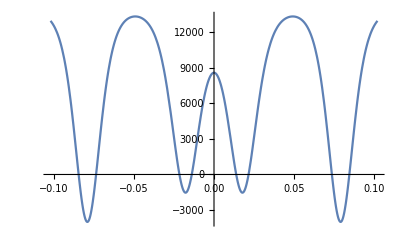

Niveis experimentais:

{4572.92,4908.,4941.7,7243.1,13840.}

Niveis obtidos pela solucao eq Schrodinger com este potencial:

{4573.36,4908.86,4942.54,7243.73,13841.5}

==========   Barion: ub==========

Raio do poco para PotCorte=13148. xCorte=0.2

Potencial obtido:

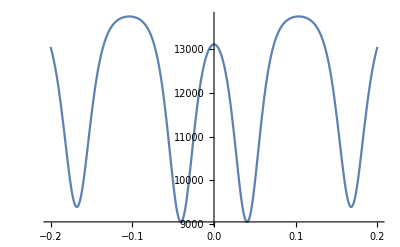

Niveis experimentais:

{11240.4,11583.8,11632.,11614.,13840.}

Niveis obtidos pela solucao eq Schrodinger com este potencial:

{11240.4,11583.8,11614.,11632.,13841.6}

==========   Barion: du==========

Raio do poco para PotCorte=10678.4 xCorte=0.114

Potencial obtido:

-Graphics-

Niveis experimentais:

{1876.54,1879.14,2231.36,4572.92,11240.4}

Niveis obtidos pela solucao eq Schrodinger com este potencial:

{1877.54,1880.15,2231.79,4573.53,11241.8}

==========   Barion: dd==========

Raio do poco para PotCorte=11042.8 xCorte=0.096

Potencial obtido:

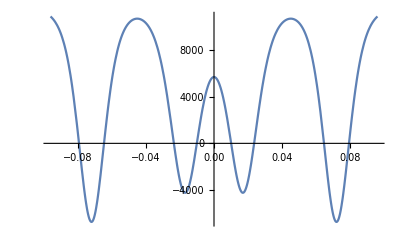

Niveis experimentais:

{1879.14,2394.9,2464.,4909.6,11624.}

Niveis obtidos pela solucao eq Schrodinger com este potencial:

{1879.61,2395.83,2464.91,4910.3,11625.4}

==========   Barion: ds==========

Raio do poco para PotCorte=11005.6 xCorte=0.096

Potencial obtido:

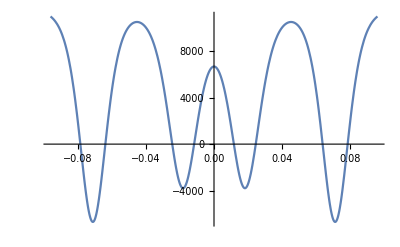

Niveis experimentais:

{2231.36,2394.9,2643.42,4941.6,11584.8}

Niveis obtidos pela solucao eq Schrodinger com este potencial:

{2232.01,2395.8,2644.11,4942.24,11586.2}

==========   Barion: dc==========

Raio do poco para PotCorte=13110. xCorte=0.102

Potencial obtido:

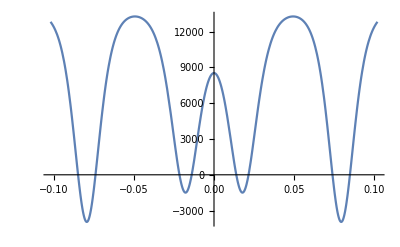

Niveis experimentais:

{4572.92,4909.6,4941.6,7239.94,13800.}

Niveis obtidos pela solucao eq Schrodinger com este potencial:

{4573.35,4910.45,4942.43,7240.56,13801.5}

==========   Barion: db==========

Raio do poco para PotCorte=19803.1 xCorte=0.098

Potencial obtido:

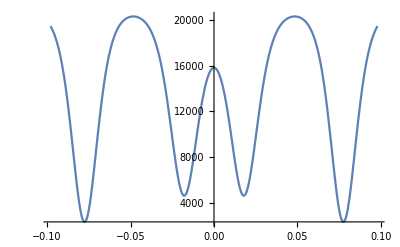

Niveis experimentais:

{11240.4,11584.8,11624.,13800.,20845.4}

Niveis obtidos pela solucao eq Schrodinger com este potencial:

{11240.9,11585.8,11624.9,13800.7,20847.4}

==========   Barion: su==========

Raio do poco para PotCorte=11004.6 xCorte=0.096

Potencial obtido:

-Graphics-

Niveis experimentais:

{2231.36,2378.74,2629.72,4941.7,11583.8}

Niveis obtidos pela solucao eq Schrodinger com este potencial:

{2232.03,2379.66,2630.4,4942.34,11585.2}

==========   Barion: sd==========

Raio do poco para PotCorte=11005.6 xCorte=0.096

Potencial obtido:

-Graphics-

Niveis experimentais:

{2231.36,2394.9,2643.42,4941.6,11584.8}

Niveis obtidos pela solucao eq Schrodinger com este potencial:

{2232.01,2395.8,2644.11,4942.24,11586.2}

==========   Barion: ss==========

Raio do poco para PotCorte=11487. xCorte=0.102

Potencial obtido:

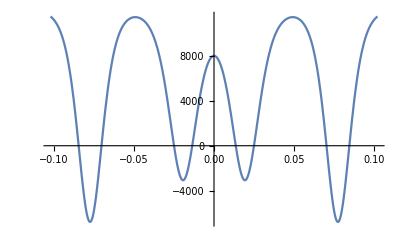

Niveis experimentais:

{2629.72,2643.42,3344.9,5387.2,12091.6}

Niveis obtidos pela solucao eq Schrodinger com este potencial:

{2630.7,2644.43,3345.36,5387.8,12093.}

==========   Barion: sc==========

Raio do poco para PotCorte=13395. xCorte=0.13

Potencial obtido:

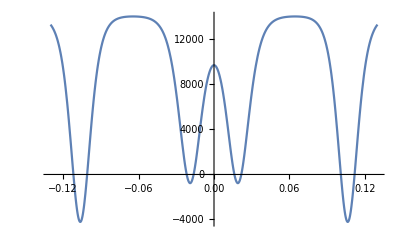

Niveis experimentais:

{5387.2,4941.7,4941.6,7580.,14100.}

Niveis obtidos pela solucao eq Schrodinger com este potencial:

{4942.54,4942.64,5387.6,7580.56,14101.6}

==========   Barion: sb==========

Raio do poco para PotCorte=19304. xCorte=0.116

Potencial obtido:

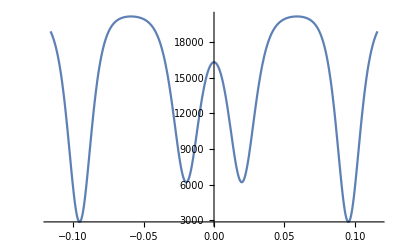

Niveis experimentais:

{11583.8,11584.8,12091.6,14100.,20320.}

Niveis obtidos pela solucao eq Schrodinger com este potencial:

{11584.6,11585.6,12091.9,14100.5,20321.9}

==========   Barion: cu==========

Raio do poco para PotCorte=13148. xCorte=0.102

Potencial obtido:

-Graphics-

Niveis experimentais:

{4572.92,4908.,4941.7,7243.1,13840.}

Niveis obtidos pela solucao eq Schrodinger com este potencial:

{4573.36,4908.86,4942.54,7243.73,13841.5}

==========   Barion: cd==========

Raio do poco para PotCorte=13110. xCorte=0.102

Potencial obtido:

-Graphics-

Niveis experimentais:

{4572.92,4909.6,4941.6,7239.94,13800.}

Niveis obtidos pela solucao eq Schrodinger com este potencial:

{4573.35,4910.45,4942.43,7240.56,13801.5}

==========   Barion: cs==========

Raio do poco para PotCorte=13395. xCorte=0.13

Potencial obtido:

-Graphics-

Niveis experimentais:

{4941.7,4941.6,5387.2,7580.,14100.}

Niveis obtidos pela solucao eq Schrodinger com este potencial:

{4942.54,4942.64,5387.6,7580.56,14101.6}

==========   Barion: cc==========

Raio do poco para PotCorte=13205. xCorte=0.116

Potencial obtido:

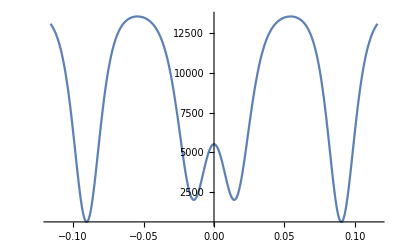

Niveis experimentais:

{5387.2,7239.94,7243.1,9590.,13900.}

Niveis obtidos pela solucao eq Schrodinger com este potencial:

{5387.3,7240.3,7243.46,9590.3,13901.6}

==========   Barion: cb==========

Raio do poco para PotCorte=20710. xCorte=0.126

Potencial obtido:

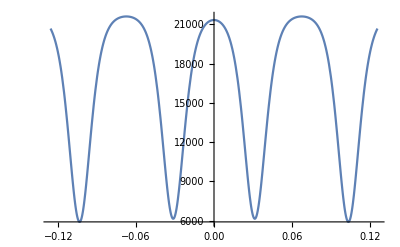

Niveis experimentais:

{13800.,13840.,13900.,14100.,21800.}

Niveis obtidos pela solucao eq Schrodinger com este potencial:

{13800.6,13840.6,13900.6,14100.6,21802.}

==========   Barion: bu==========

Raio do poco para PotCorte=13148. xCorte=0.2

Potencial obtido:

-Graphics-

Niveis experimentais:

{11240.4,11583.8,11614.,11632.,13840.}

Niveis obtidos pela solucao eq Schrodinger com este potencial:

{11240.4,11583.8,11614.,11632.,13841.6}

==========   Barion: bd==========

Raio do poco para PotCorte=19803.1 xCorte=0.098

Potencial obtido:

-Graphics-

Niveis experimentais:

{11240.4,11584.8,11624.,13800.,20845.4}

Niveis obtidos pela solucao eq Schrodinger com este potencial:

{11240.9,11585.8,11624.9,13800.7,20847.4}

==========   Barion: bs==========

Raio do poco para PotCorte=19304. xCorte=0.116

Potencial obtido:

-Graphics-

Niveis experimentais:

{11583.8,11584.8,12091.6,14100.,20320.}

Niveis obtidos pela solucao eq Schrodinger com este potencial:

{11584.6,11585.6,12091.9,14100.5,20321.9}

==========   Barion: bc==========

Raio do poco para PotCorte=20710. xCorte=0.126

Potencial obtido:

-Graphics-

Niveis experimentais:

{13800.,13840.,13900.,14100.,21800.}

Niveis obtidos pela solucao eq Schrodinger com este potencial:

{13800.6,13840.6,13900.6,14100.6,21802.}

==========   Barion: bb==========

Raio do poco para PotCorte=27304.9 xCorte=0.076

Potencial obtido:

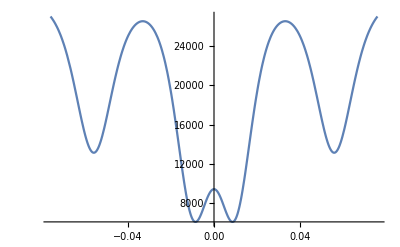

Niveis experimentais:

{11614.,20320.,20845.4,21800.,28742.}

Niveis obtidos pela solucao eq Schrodinger com este potencial:

{11614.5,20321.,20846.,21801.7,28744.5}

ResHEP1.csv

```mathematica
NivCalc=5;
For[ii=1,ii≤Length[BarDat],ii++,
NivElem=BarDat[[ii]];
PotCorte=Evaluate[PorcCorte*NivElem[[NivCalc]]];

Print["==========   Barion: ",BarTit[[ii]],"=========="];
V=dressingTransformationPotentials[NivElem,PotxMax];
xCorte=PotxMax;
While [(xCorte>0.0)&&(PotCorte<V[xCorte]),xCorte=xCorte-xstep];
Print["Raio do poco para PotCorte=",PotCorte," xCorte=",xCorte];
Print["Potencial obtido:"];
Print[Plot[V[Abs[x]],{x,-xCorte,xCorte},PlotRange->All]];
Print["Niveis experimentais:"];
Print[NivElem];
ndse=NDEigensystem[-ψ''[x]+V[Abs[x]] ψ[x],ψ,{x,-PotxMax,PotxMax},NivCalc,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{"MaxCellMeasure"->0.005}}}}];
Print["Niveis obtidos pela solucao eq Schrodinger com este potencial:"];
Print[ndse[[1]]];
WriteString[matout,"\n===== Barion ",BarTit[[ii]]," =====; \n"];
WriteString[matout,"Energia=; ",ToString[BarDat[[ii,5]],InputForm],"; \n"];
WriteString[matout,"xCorte=; ",ToString[xCorte,InputForm],"; \n\n"];
lista={"x; Pot; "};
For[i=1,i<=NivCalc,i++,lista=Append[lista,StringJoin["Psi",ToString[i,InputForm],"; "]]];
lista=Append[lista,"\n"];
Cabec=StringJoin[lista];
WriteString[matout,Cabec];
Do[
lista={};
lista=Append[lista,StringJoin[ToString[x,InputForm],"; ",ToString[V[Abs[x]],InputForm],"; "]];
For[i=1,i<=NivCalc,i++,lista=Append[lista,StringJoin[StringJoin[ToString[ndse[[2,i]][x],InputForm],"; "]]]];
lista=Append[lista,"\n"];
Cabec=StringJoin[lista];
WriteString[matout,Cabec],{x,-xCorte,xCorte,xCorte/NumRegArq}];

]
Close[matout]
```